# Rational minimax iterations for the pth root

This notebook demonstrates a few results from “Rational Minimax Iterations for Computing the Matrix pth Root” by Evan S. Gawlik in Constructive Approximation, 54, 1-34, (2021).

```mathematica
Needs["FunctionApproximations`"];
```

## Rational approximation of x^(1/2)

The best rational approximant (in the relative minimax sense) of the function x^(1/2) on a positive real interval obeys an interesting recursion under composition [1].  Let R_(m,l) denote the set of all rational functions of type (m,l)---ratios of polynomials of degree at most m to polynomials of degree at most l.  Let α ∈ (0,1) and

r_(m,l)(·,α)=argmin_(r∈R_(m,l))max_(α^2≤x≤1)|(r(x)-x^(1/2))/x^(1/2)|.

Let (r̂)_(m,l)(x,α) be the unique scalar multiple of r_(m,l)(x,α) satisfying

min_(α^2≤x≤1) ((r̂)_(m,l)(x,α)-x^(1/2))/x^(1/2) = 0.

Then, for any positive integers m and m’, the relation

(r̂)_(m,m)(x,α) (r̂)_(m',m')(x/((r̂)_(m,m)(x,α))^2,α') = (r̂)_(m'',m'')(x,α)

holds with m’’ = 2mm’+m’+m and α’ = α/((r̂)_(m,m)(α^2,α)).  An analogous recursion holds for (r̂)_(m,m-1)(x,α):
(r̂)_(m,m-1)(x,α) (r̂)_(m',m'-1)(x/((r̂)_(m,m-1)(x,α))^2,α') = (r̂)_(m'',m''-1)(x,α),

where m’’ = 2mm’ and α’ = α/((r̂)_(m,m-1)(α^2,α)).  
The key takeaway from these recursions is that high-degree best rational approximants of x^(1/2)can be constructed by carefully composing low-degree best rational approximants of x^(1/2).

Let us illustrate the recursion (Title) for (r̂)_(m,m)(x,α).  First, we plot the relative error ((r̂)_(m,m)(x,α)-x^(1/2))/x^(1/2) with α = 10^-3 and m = 2.

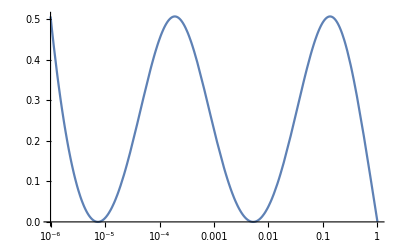

```mathematica
r[m_,l_,x_,alpha_]:=MiniMaxApproximation[z^(1/2), {z, {alpha^2,1}, m, l}, 
     MaxIterations -> 200, WorkingPrecision -> 50][[2]][[1]]/.z->x;
rhat[m_,l_,x_,alpha_]:=r[m,l,x,alpha]/(2-r[m,l,alpha^2,alpha]/alpha);
alpha =10^-3;
m=2;
LogLinearPlot[Evaluate[(rhat[m,m,x,alpha]-x^(1/2))/x^(1/2)],{x,alpha^2,1}]
```

The relative error equioscillates 2m + 2 times on [α^2,1], which is a manifestation of the well-known equioscillation theorem characterizing best rational approximants of continuous functions on real intervals [2].  (Here it oscillates around a small positive number rather than around zero since we have plotted the relative error committed by r̂ rather than r.)  Now let us illustrate the behavior of (r̂)_(m,m)(x,α) under composition.

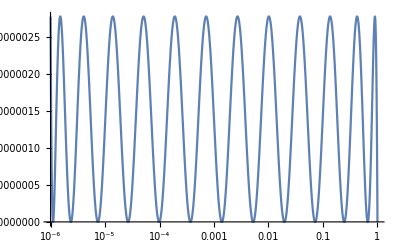

```mathematica
alphaprime=alpha/rhat[m,m,alpha^2,alpha];
mprime=2;
g[x_]:=rhat[m,m,x,alpha]*rhat[mprime,mprime,x/rhat[m,m,x,alpha]^2,alphaprime];
LogLinearPlot[Evaluate[(g[x]-x^(1/2))/x^(1/2)],{x,alpha^2,1}]
```

The relative error equioscillates 2m’’+2 times on [α^2,1], where m’’ = 2mm’+m’+m.  Compare this with the best rational approximant of type (m’’,m’’):

```mathematica
mdoubleprime=2m*mprime+mprime+m;
LogLinearPlot[Evaluate[(rhat[mdoubleprime,mdoubleprime,x,alpha]-x^(1/2))/x^(1/2)],{x,alpha^2,1}]
```

-Graphics-

The plot is identical, as predicted by the recursion (Title).

## Rational approximation of x^(1/p)

It turns out that best rational approximants of x^(1/p) (where p>2 is an integer) behave similarly to best rational approximants of x^(1/2) under composition, in the sense that the relative error committed by a suitable composition of best rational approximants of x^(1/p)will equioscillate (but the number of equioscillation points will not be high enough to ensure optimality, in general) [3].

Generalizing the notation from above, let α ∈ (0,1) and

r_(m,l,p)(·,α)=argmin_(r∈R_(m,l))max_(α^p≤x≤1)|(r(x)-x^(1/p))/x^(1/p)|.

Let (r̂)_(m,l,p)(x,α) be the unique scalar multiple of r_(m,l,p)(x,α) satisfying

min_(α^p≤x≤1) ((r̂)_(m,l,p)(x,α)-x^(1/p))/x^(1/p) = 0.

In view of our earlier observations about the case p = 2, it is natural to consider for p > 2 the composition

g(x) = (r̂)_(m,l,p)(x,α) (r̂)_(m',l',p)(x/((r̂)_(m,l,p)(x,α))^p,α'),

where α’ = α/((r̂)_(m,l,p)(α^p,α)) and m’, l’ are positive integers.  Below we plot the relative error (g(x)-x^(1/p))/x^(1/p) for certain choices of m, l, m’, l’, p, α.

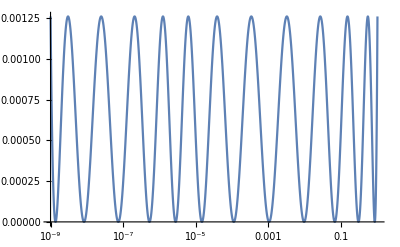

```mathematica
r[m_,l_,p_,x_,alpha_]:=MiniMaxApproximation[z^(1/p), {z, {alpha^p,1}, m, l}, 
     MaxIterations -> 200, WorkingPrecision -> 50][[2]][[1]]/.z->x;
rhat[m_,l_,p_,x_,alpha_]:=r[m,l,p,x,alpha]/(2-r[m,l,p,alpha^p,alpha]/alpha);
p=3;
alpha =10^-3;
m=2;
l=1;
alphaprime=alpha/rhat[m,l,p,alpha^p,alpha];
mprime=3;
lprime=2;
g[x_]:=rhat[m,l,p,x,alpha]*rhat[mprime,lprime,p,x/rhat[m,l,p,x,alpha]^p,alphaprime];
LogLinearPlot[Evaluate[(g[x]-x^(1/p))/x^(1/p)],{x,alpha^p,1}]
```

Notice that the relative error equioscillates.  It can be shown that in general (g(x)-x^(1/p))/x^(1/p) equioscillates (m+l+1)(m'+l'+1)+1 times, which is high but not optimal unless p = 2, l ∈ {m-1,m}, and l' ∈ {m'-1,m'}.

## Iteration

The observations above suggest the following iteration for computing high-degree rational approximants of x^(1/p) with small relative error on [α^p,1], where α ∈(0,1):

f_(k+1)(x)=f_k(x)(r̂)_(m,l,p)(x/(f_k(x))^p,α_k),		f_0(x)=1,
α_(k+1)=α_k/((r̂)_(m,l,p)(α_k^p,α_k)),				α_0=α.

Here is an illustration of how the iteration performs.

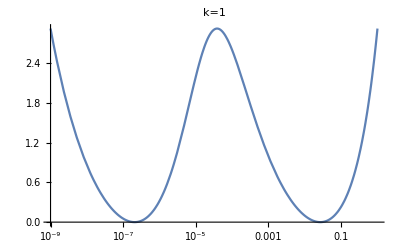

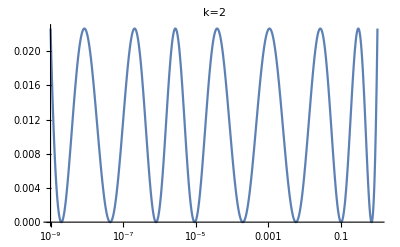

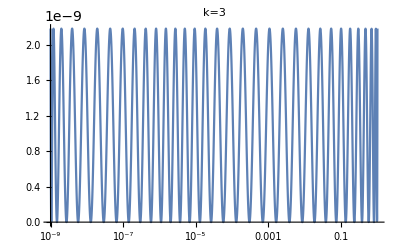

```mathematica
f[0,x_]:=1;
f[k_,x_]:=f[k-1,x]rhat[m,l,p,x/f[k-1,x]^p,alpha[k-1]];
Clear[alpha];
alpha[k_]:=alpha[k-1]/rhat[m,l,p,alpha[k-1]^p,alpha[k-1]];
alpha[0] =10^-3;
p=3;
m=2;
l=1;
For[k=1,k≤3,k++,Print[LogLinearPlot[Evaluate[(f[k,x]-x^(1/p))/x^(1/p)],{x,alpha[0]^p,1},PlotLabel->StringJoin["k=",ToString[k]]]]]
```

In just three iterations, the maximum relative error max_(α^p≤x≤1) |(f_k(x)-x^(1/p))/x^(1/p)| has been reduced to near zero.  In fact, it converges monotonically to zero as k→∞ with order of convergence m+l+1 [3].  Furthermore, at each step k, the relative error (f_k(x)-x^(1/p))/x^(1/p) equioscillates (m+l+1)^k+1 times on [α^p,1], as can be seen above.

The rapid uniform convergence of f_k(x) to x^(1/p)on [α^p,1] can be leveraged for many purposes.  One application is the computation of matrix pth roots.  Roughly speaking, if a square matrix A has spectrum in or near [α^p,1], then f_k(A) yields a good approximation of A^(1/p).  Since f_kcan be constructed iteratively, so too can f_k(A).  Details can be found in [3].  Another application is approximation theoretic.  One can leverage f_k(x) to construct rational approximants of x^(1/p) with small uniform error (in the absolute sense) on [0,1] (as opposed to [α^p,1]) using a clever choice of α depending on p and k.  This construction can then be used to prove approximation theoretic results for compositions of rational functions.  The results are analogous to the famous root-exponential convergence of rational approximants of x^(1/p)on [0,1] [4], but they concern compositions of rational functions rather than general rational functions.  The interested reader is referred to [5] for more details.

## References

[1] E. S. Gawlik.  Zolotarev Iterations for the Matrix Square Root.  SIAM Journal on Matrix Analysis and Applications, 40(2), 696-719 (2019).
[2] L. N. Trefethen.  Approximation Theory and Approximation Practice.  Vol. 164.  SIAM (2019).
[3] E. S. Gawlik.  Rational Minimax Iterations for Computing the Matrix pth Root.  Constructive Approximation, 54, 1-34, (2021).
[4] H. R. Stahl. Best Uniform Rational Approximation of x^α on [0, 1]. Acta Mathematica, 190(2):241– 306, 2003.
[5] E. S. Gawlik & Y. Nakatsukasa. Approximating the pth Root by Composite Rational Functions. Journal of Approximation Theory, 266, 105577 (2021).